## 1. Постановка задачі

Задача Діріхле для еліптичного рівняння на двовимірній області 

	L[u] = -μΔu + β∇u +σu = f		Ω=[0,1]x[0,1]			(1)
				u|_Γ = 0						(2)
				
Ми розглядаємо задачу зі сталими коефіцієнтами, тому 


	u=(x,y),	f=f(x,y),	μ=const,   β=const,   σ=const.		(3)

```mathematica
(* Блок ініціалізації вхідних параметрів *)
μ=Function[{x,y},100];
β=Function[{x,y},1];
σ=Function[{x,y},1];
f=Function[{x,y},100000];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
$pathToFile="square.node";
stmp = OpenWrite[$pathToFile];

WriteString[stmp,"8 2 0 0 \n"];

(* == <vertex #> <x> <y> [attributes] [boundary marker] *)
WriteString[stmp, "1 0.0 0.0 \n"];
WriteString[stmp, "2 0.5 0.0 \n"];
WriteString[stmp, "3 1.0 0.0 \n"];
WriteString[stmp, "4 1.0 0.5 \n"];
WriteString[stmp, "5 1.0 1.0 \n"];
WriteString[stmp, "6 0.5 1.0 \n"];
WriteString[stmp, "7 0.0 1.0 \n"];
WriteString[stmp, "8 0.0 0.5"];
Close[stmp];
```

### Execution of triangulation program

```mathematica
$triangleCmd= "./triangle ";
commandToRun =$triangleCmd<>"square.node";
Run[commandToRun];
```

### Data input

```mathematica
triangles=Import["square.1.ele","Table"];
(*Results in list of vetrices forming triangles*)
triangles=Delete[triangles,-1];
triangles=Delete[triangles,1];
For[i=1,i<=Length[triangles],i++,
triangles[[i]]=Delete[triangles[[i]],1]
];
triangles;


nodes=Import["square.1.node","Table"];
(*Results in list of vetrices*)
nodes=Delete[nodes,-1];
nodes=Delete[nodes,1];
For[i=1,i<=Length[nodes],i++,
nodes[[i]]=Delete[nodes[[i]],1];
];

Print["Nodes are: ", nodes];
```

Nodes are: {{0,0,1},{0.5,0,1},{1,0,1},{1,0.5,1},{1,1,1},{0.5,1,1},{0,1,1},{0,0.5,1}}

### Visualization

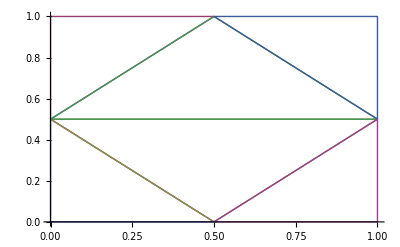

```mathematica
(*make list of edges grouped by triangles [[tris]] 
and ListLinePlot[{tris[[1]],..,tris[[n]]] them.*)

getVertexXY:=Function[{triangleNumber,vertexNumber},
Delete[nodes[[triangles[[triangleNumber,vertexNumber]]]],-1]
];
(*list of triangle vertecies for complete triangle drawing*)
toFormTriangle={1,2,3,1};

(* array of triangles *)
tris={{}};
For[i=1,i<=Length[triangles],i++,
self={{}};
For[j=1,j<=Length[toFormTriangle],j++,
self=Append[self,getVertexXY[i,toFormTriangle[[j]]]];
];
self=Delete[self,1];
tris=Append[tris,self];
]
tris=Delete[tris,1];

ListLinePlot[tris]
```

```mathematica
Length[tris]
```

6

-----------------------------------------------------FEM Procedure----------------------------------------------------

```mathematica
(* number of the finite elements *) 
nel=6; 
(* number of nods of triangulation *) 
nod=8;
(* nod quantity of finite element *) 
nodTriangl=3;
(* number of boundary nods *)
numBoundCond=8;
(* number of boundary nods with Dirichlets BC *)
nodDirichl=8;
(* list of equation numbers *)
neq=Table[0,{i,1,nod}];
(* list of boundary point numbers of equations *)
boundpoint={1,2,3,4,5,6,7,8};
Boundsort=Sort[boundpoint];Print[Boundsort]




(*   ========   Order of equations   ========    *)
  i=nv=0;m=1;k=0;For[i=1,i≤nod,i++,If[i≠Boundsort⟦m⟧,neq⟦i⟧=nv=nv+1,{neq⟦i⟧=k=k-1,If[m<numBoundCond,m=m+1]}]];
Print["neq=",neq,"  nv=",nv,"  k=",k];
(*   ========   Bandwidth of matrix   ========    *)
gband=0;
For[e=1,e≤nel,e++,For[l=1,l<3,l++,n=triangles⟦e,l⟧;equat=neq⟦n⟧;If[equat>0,For[m=l+1,m≤3,m++,k=triangles⟦e,m⟧;colum=neq⟦k⟧;
If[colum>0,i=Abs[equat-colum];If[i>gband,gband=i]];
]]]];Print["Bandwidth of matrix=",2*gband+1];







matrix=Table[0.,{i,1,nv},{j,1,nv}];
vektor=Table[0.,{i,1,nv}];
width=2*gband+1
matX=Table[0.,{i,1,nv},{j,1,width}];
vekR=Table[0.,{i,1,nv}];
(*   ========   Loop of  finite elements   ========  *)
For[e=1,e≤nel,e++,
i=tris⟦e,1⟧;j=tris⟦e,2⟧;m=tris⟦e,3⟧;
bi=nodes⟦j,2⟧-nodes⟦m,2⟧;ci=nodes⟦m,1⟧-nodes⟦j,1⟧;
bj=nodes⟦m,2⟧-nodes⟦i,2⟧;cj=nodes⟦i,1⟧-nodes⟦m,1⟧;
bm=nodes⟦i,2⟧-nodes⟦j,2⟧;cm=nodes⟦j,1⟧-nodes⟦i,1⟧;
dt=bi*cj-bj*ci;
ke=1./dt*({{bi*bi+ci*ci, bi*bj+ci*cj, bi*bm+ci*cm}, {bi*bj+ci*cj, bj*bj+cj*cj, bj*bm+cj*cm}, {bm*bi+cm*ci, bm*bj+cm*cj, bm*bm+cm*cm}});
xs=1/3.*(nodes⟦m,1⟧+nodes⟦j,1⟧+nodes⟦i,1⟧);ys=1/3.*(nodes⟦m,2⟧+nodes⟦j,2⟧+nodes⟦i,2⟧);
me=ω^2*dt/24.*({{2., 1., 1.}, {1., 2., 1.}, {1., 1., 2.}});fe=dt/6.*f[xs,ys]*({{1.}, {1.}, {1.}});
(*Print["e=",e," dt=",dt,"  determinant K_e=",Det[ke]];*)
(*   ===    Assembling of FEM equations    =====   *)
For[i=1,i≤nodTriangl,i++,
n=tris⟦e,i⟧;equat=neq⟦n⟧;
If[equat>0,
For[j=1,j≤nodTriangl,j++,
k=tris⟦e,j⟧;colomn=neq⟦k⟧;
If[colomn>0,
matrix⟦equat,colomn⟧=matrix⟦equat,colomn⟧+ke⟦i,j⟧]
];
vektor⟦equat⟧=vektor⟦equat⟧+fe⟦i,1⟧]
]; 
(*   ========    Assembling of FEM equations    ========   *)
For[i=1,i≤nodTriangl,i++,
n=tris⟦e,i⟧;equat=neq⟦n⟧;
If[equat>0,
For[j=1,j≤nodTriangl,j++,
k=tris⟦e,j⟧;colomn=neq⟦k⟧;
If[colomn>0,pl=colomn-equat+gband+1;
matX⟦equat,pl⟧=matX⟦equat,pl⟧+ke⟦i,j⟧]
];
vekR⟦equat⟧=vekR⟦equat⟧+fe⟦i,1⟧]
]];Print["  matrix=",MatrixForm[matrix],"  vektor=",MatrixForm[vektor]];    Print["  matrix=",MatrixForm[matX],"  vektor=",MatrixForm[vekR]];   
(*    ====   Solving of FEM equations   =====   *)
q=LinearSolve[matrix,vektor];
(*    ====   Postprocesoring of FEM   ===    *)
(*    ====   Nods Values of FEM Approximation   ===    *)
PointValues=Table[{nodes⟦i,1⟧,nodes⟦i,2⟧,0.},{i,1,nod}];

Print["  FEM Approximation Values at the Triangulation Nodes=",PointValues];
Print[√NormaH1];
```

{1,2,3,4,5,6,7,8}

neq={-1,-2,-3,-4,-5,-6,-7,-8}  nv=0  k=-8

Bandwidth of matrix=1

1

Part::pspec: Part specification {0.5, 0} is neither an integer nor a list of integers.

Part::pspec: Part specification {0, 0.5} is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Part::partd: Part specification {{0, 0, 1}, {0.5, 0, 1}, {1, 0, 1}, {1, 0.5, 1}, {1, 1, 1}, {0.5, 1, 1}, {0, 1, 1}, {0, 0.5, 1}} ⟦ {0, 0}, 2 ⟧ is longer than depth of object.

Part::partd: Part specification {{0, 0, 1}, {0.5, 0, 1}, {1, 0, 1}, {1, 0.5, 1}, {1, 1, 1}, {0.5, 1, 1}, {0, 1, 1}, {0, 0.5, 1}} ⟦ {0, 0}, 1 ⟧ is longer than depth of object.

Part::partd: Part specification {{0, 0, 1}, {0.5, 0, 1}, {1, 0, 1}, {1, 0.5, 1}, {1, 1, 1}, {0.5, 1, 1}, {0, 1, 1}, {0, 0.5, 1}} ⟦ {0, 0}, 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {1./-{« 8 »} ⟦ {« 2 »}, 1 ⟧\ (Part[« 3 »] + Times[« 2 »]) - (Times[« 2 »] + Part[« 3 »])\ {« 8 »} ⟦ {« 2 »}, 2 ⟧, 1./-{« 8 »} ⟦ {« 2 »}, 1 ⟧\ (Part[« 3 »] + Times[« 2 »]) - (Times[« 2 »] + Part[« 1 »])\ « 1 »}\ {« 1 »} cannot be combined.

Thread::tdlen: Objects of unequal length in 100\ {0.0416667\ (-{{« 3 »}, {« 3 »}, {« 3 »}, {« 3 »}, {« 3 »}, {« 3 »}, {« 3 »}, {« 3 »}} ⟦ {1, 0.5}, 1 ⟧\ ({« 8 »} ⟦ {« 2 »}, 2 ⟧ - Part[« 3 »]) - (-Part[« 3 »] + {« 8 »} ⟦ {« 2 »}, 1 ⟧)\ « 1 »), 0.0416667\ (« 1 »)}\ {{2., 1., 1.}, {1., 2., 1.}, {1., 1., 2.}} cannot be combined.

Thread::tdlen: Objects of unequal length in {0.166667\ (-{{« 3 »}, {« 3 »}, {« 3 »}, {« 3 »}, {« 3 »}, {« 3 »}, {« 3 »}, {« 3 »}} ⟦ {1, 0.5}, 1 ⟧\ ({« 8 »} ⟦ {« 2 »}, 2 ⟧ - Part[« 3 »]) - (-Part[« 3 »] + {« 8 »} ⟦ {« 2 »}, 1 ⟧)\ {{« 3 »}, {« 3 »}, {« 3 »}, {« 3 »}, {« 3 »}, {« 3 »}, {« 3 »}, {« 3 »}} ⟦ {1, 0.5}, 2 ⟧), « 20 »\ (« 1 » - « 1 »)}\ « 6 » « 1 » {« 1 »} cannot be combined.

General::stop: Further output of Thread :: tdlen will be suppressed during this calculation.

matrix={}  vektor={}

matrix={}  vektor={}

LinearSolve::matrix: Argument {} at position 1 is not a non-empty rectangular matrix.

FEM Approximation Values at the Triangulation Nodes={{0,0,0.},{0.5,0,0.},{1,0,0.},{1,0.5,0.},{1,1,0.},{0.5,1,0.},{0,1,0.},{0,0.5,0.}}

12266.3